```mathematica
URN[a_,b_,c_,d_,e_]:=
Module[{NN=a, f0=b,f=c, r=d, seed=e, Q, S},
Q=f0; S=0;
SeedRandom[seed];
While[ Q>0,
If[ RandomReal[]≤(NN-S)/NN,
If[RandomReal[]≤r,
(*Q=Q+Pare[0.5,RandomReal[],10000,1]-1; S=S+1,Q=Q-1*)
(*Q=Q+f-1; S=S+1,Q=Q-1*)
Q=Q+RandomInteger[{1,199}]-1; S=S+1,Q=Q-1
],
Q=Q-1
]
];
S (* S = final cascade size *)
]

Pare[a_, u_,h_,l_]:=(-(u*h^a-u*l^a-h^a)/(h*l)^a)^(-1/a);
For[j=0, j<6, j++,
r = 0.01 +j * 0.0004;
f1[i_]:=URN[500000, 100, 100, r,i];
data=Parallelize[Map[f1, Range[1,1000]]];
(*Print[data]*);
Print["r=",r,
",  UD max=", 
N[Max[Select[data,#<10000&]]],
",  SD len=", 
N[Length[Select[data,#>10000&]]],
",  SD mean=", 
N[Mean[Select[data,#>10000&]]],
",  SD sd=",
N[StandardDeviation[Select[data,#>10000&]]]
];
Print[Histogram[data,{0,200000,2000},ScalingFunctions->"Log"]]
]
```

StandardDeviation::shlen: 引数{24680}は少なくとも2つの要素を持っていなければなりません．

StandardDeviation::shlen: 引数{24680.}は少なくとも2つの要素を持っていなければなりません．

r=0.01,  UD max=5981.,  SD len=1.,  SD mean=24680.,  SD sd=StandardDeviation[{24680.}]

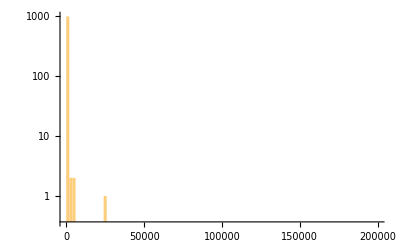

r=0.0104,  UD max=6402.,  SD len=2.,  SD mean=49926.5,  SD sd=35784.6

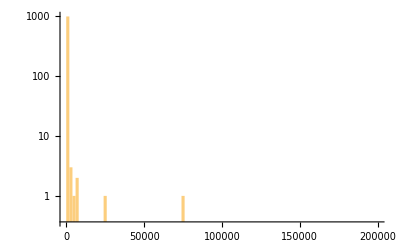

r=0.0108,  UD max=6951.,  SD len=5.,  SD mean=79357.2,  SD sd=15234.6

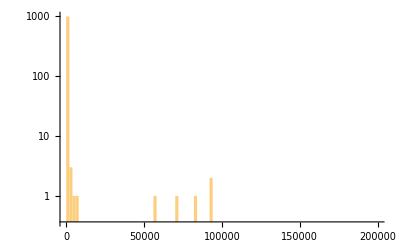

r=0.0112,  UD max=9386.,  SD len=11.,  SD mean=108152.,  SD sd=13771.7

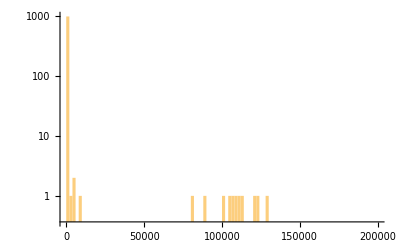

r=0.0116,  UD max=1879.,  SD len=17.,  SD mean=133110.,  SD sd=12266.6

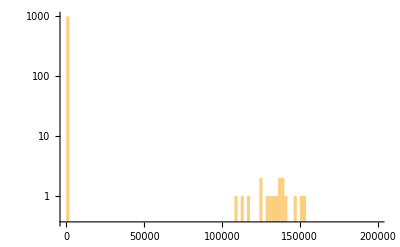

r=0.012,  UD max=3640.,  SD len=19.,  SD mean=156096.,  SD sd=10267.8

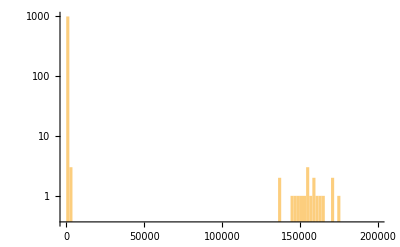

```mathematica
Pareto
```

r=0.01,  UD max=9418.,  SD len=5.,  SD mean=12779.6,  SD sd=843.641

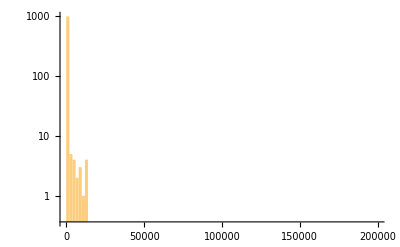

r=0.0104,  UD max=9670.,  SD len=74.,  SD mean=37424.3,  SD sd=4608.12

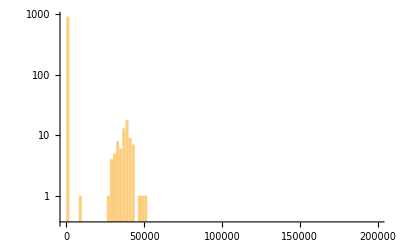

r=0.0108,  UD max=677.,  SD len=142.,  SD mean=71912.7,  SD sd=2896.83

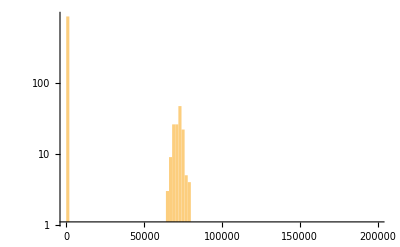

r=0.0112,  UD max=306.,  SD len=213.,  SD mean=103134.,  SD sd=2407.39

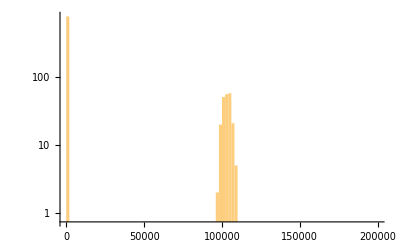

r=0.0116,  UD max=145.,  SD len=257.,  SD mean=131369.,  SD sd=2109.34

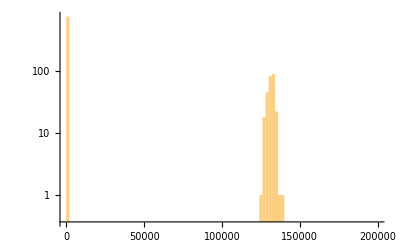

r=0.012,  UD max=120.,  SD len=309.,  SD mean=156892.,  SD sd=1755.96

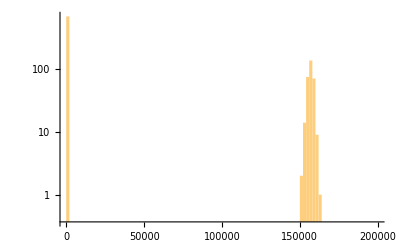

```mathematica
fixed
```

r=0.01,  UD max=9384.,  SD len=6.,  SD mean=12991.2,  SD sd=2229.01

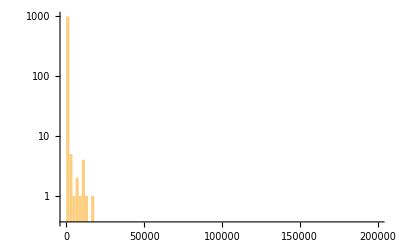

r=0.0104,  UD max=5534.,  SD len=48.,  SD mean=37433.8,  SD sd=5537.07

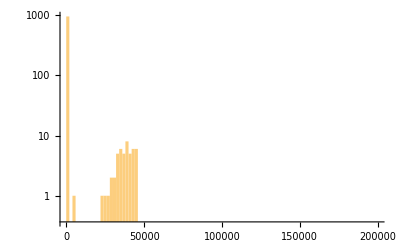

r=0.0108,  UD max=597.,  SD len=115.,  SD mean=72197.8,  SD sd=3989.22

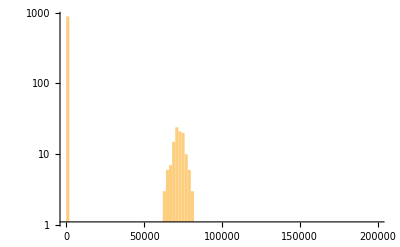

r=0.0112,  UD max=383.,  SD len=159.,  SD mean=103097.,  SD sd=3132.28

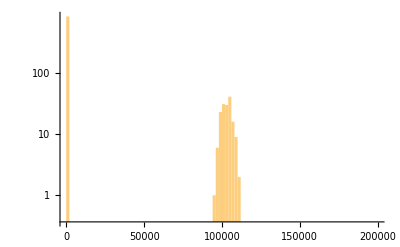

r=0.0116,  UD max=429.,  SD len=200.,  SD mean=131208.,  SD sd=2570.42

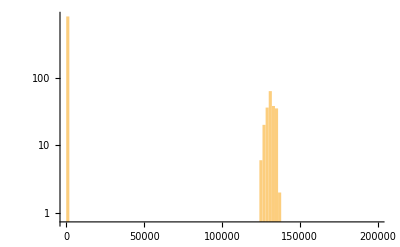

r=0.012,  UD max=150.,  SD len=238.,  SD mean=156846.,  SD sd=2397.33

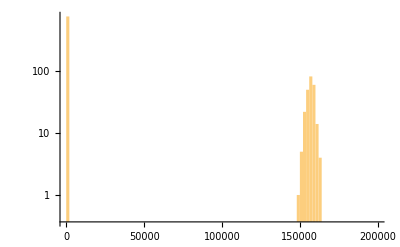

```mathematica
uniform
```

```mathematica
Pare[a_, u_,h_,l_]:=(-(u*h^a-u*l^a-h^a)/(h*l)^a)^(-1/a);
MeanPare[a_, h_,l_]:=l^a/(1-(l/h)^a)*a/(a-1)*(1/l^(a-1)-1/h^(a-1));
N[MeanPare[0.5,10000,1]]
```

100.